### Values of Z versus U (by hand)

These are some results I obtained by quickly doing a small momentum grid, high temperature (T=t).

```mathematica
(* Import the files *)
SetDirectory[NotebookDirectory[]];
ZList019=Import["Z_vs_U_lambda=0.19.dat"];


(* The fit of this Z(U) is polynomial *)
Clear[a,b,c,d,x]
Zf=NonlinearModelFit[ZList019,a+b*x^2+c*x^4+d*x^6,{a,b,c,d},x]
```

FittedModel[1.09639-0.00288744 x^2+0.000532206 x^4-3.35321×10^-6 x^6]

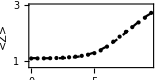

```mathematica
FigZ=Show[ListPlot[ZList019,
Frame->True,
ImageSize->160,
AspectRatio->0.5,
PlotRange->{Automatic,{0.8,3}},
PlotStyle->{{PointSize[Large],Black}},
FrameLabel->{Style["U/t",10,Black,FontFamily->"Latin Modern Roman"],
Style["<Z>",10,Black,FontFamily->"Latin Modern Roman"]},
FrameTicks->{{{1,2,3},None},Automatic},
FrameTicksStyle->Directive[10,Black,FontFamily->"Latin Modern Roman"]],Plot[Zf[x],{x,0,10},PlotStyle->{{Black,Dashed}}]]
```

```mathematica
FigZ=
Show[ListPlot[ZList019,
Frame->True,
ImageSize->120,
PlotRange->{Automatic,Automatic},
PlotStyle->{{PointSize[Medium],Black}},
FrameTicksStyle->Directive[10,Black,FontFamily->"Latin Modern Roman"]],Plot[Zf[x],{x,0,10},PlotStyle->{{Black,Dashed}}],
Graphics[{Text[Style["<Z>",10,Black,FontFamily->"Latin Modern Roman"],{0.2,2.9},{-1,1}],
Text[Style["U/t",10,Black,FontFamily->"Latin Modern Roman"],{8,0.5}]}]]
```

-Graphics-

### Fig 3: Tc versus U

```mathematica
(* Import the files *)
SetDirectory[NotebookDirectory[]];
TcListλ0=Import["Tc_vs_U_lambda=0.dat"];
TcListλ19=Import["Tc_vs_U_lambda=0.19_spm.dat"];
TcListλ19d=Import["Tc_vs_U_lambda=0.19_d.dat"];
(* The perfect forward scattering limit *)
Ω=100; (* meV *)
kB=0.08617; (* K per meV *)
```

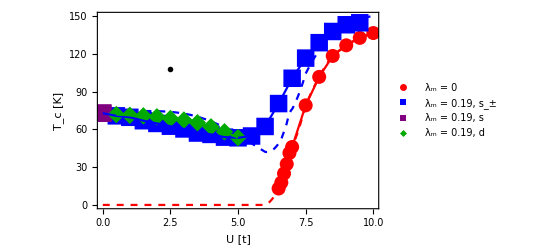

```mathematica
(* Make the plot *)
λx=0.19;
ps=18;
TcvsU=Interpolation[Join[Table[{U,0},{U,0,6,0.1}],TcListλ0],InterpolationOrder->2];
Fig3=Show[
Plot[{TcvsU[U],
TcvsU[U]+λx/(2*(Zf[U])^2+3*λx)*Ω/kB},{U,0,11},
PlotRange->{{0,10},{0,150}},
Frame->True,
ImageSize->400,
FrameLabel->{Style["U [t]",16,Black,FontFamily->"Latin Modern Roman"],
Style["T_c [K]",16,Black,FontFamily->"Latin Modern Roman"]},
FrameTicksStyle->Directive[14,Black,FontFamily->"Latin Modern Roman"],
PlotStyle->{{Dashed,Red},{Dashed,Blue}},
Epilog->Inset[FigZ,{2.5,108}]],
ListPlot[{TcListλ0,TcListλ19[[2;;Length[TcListλ19]]],TcListλ19[[1;;1]],TcListλ19d},
Frame->True,
ImageSize->400,
PlotRange->{{0,10},{0,150}},
PlotStyle->{Red,Blue,Purple,Darker[Green]},
PlotMarkers->{{"●",Offset[ps*0.8]},{"■",Offset[ps]},{"■",Offset[ps]},{"◆",Offset[ps]}},
PlotLegends->Placed[PointLegend[{Style["λ_m = 0",Black,14,FontFamily->"Latin Modern Roman"],Style["λ_m = 0.19, s_±",Black,14,FontFamily->"Latin Modern Roman"],
Style["λ_m = 0.19, s",Black,14,FontFamily->"Latin Modern Roman"],
Style["λ_m = 0.19, d",Black,14,FontFamily->"Latin Modern Roman"]},
LegendLayout->{"Column",2}],{0.31,0.14}]
],
ListLinePlot[{TcListλ0,TcListλ19,TcListλ19[[1;;1]],TcListλ19d},
PlotStyle->{Red,Blue,Purple,Darker[Green]},
PlotRange->{{0,10},{0,140}}
]
]
Export["Figure3.pdf",Fig3];
```